```mathematica
SetDirectory[NotebookDirectory[]];
{ti, tf, dt}={0.001,2 π*10+ti, dt=(tf-ti)/1};
{αi,αf,dα} = {π/4,π/4,1};
{βi,βf,dβ}={π/4,π/4,1};

a0=1.;
(* q=10^-19;
h=1.054571800 10^-34;
c=3 10^8; *)
me=ϵ0=1;
q=h=c=1;
e=1;
a10=1.;
a20=1.;
ωf1=1.;
ωf2=0.5;
t0=30.;
τ=20.;
neq=3;
nmax=3;
m[m1_, m2_]:=m1-m2;
int[n1_, l1_, n2_, l2_ , l_, t_]:=int[n1, l1, n2, l2, l, t];
R[n_, l_,r_]:=1/(√(2 n (n-l-1)! (n+l)!)) (2/(n a0))^(3/2) ⅇ^(-r/(n a0))((2 r)/(n a0))^l LaguerreL[n-l-1,2 l+1, (2 r)/(n a0)];
Y[l_, m_, θ_, ϕ_]:=I^l SphericalHarmonicY[l, m,θ, ϕ];
a1[t_]:=a10 Exp[-(t-t0)^2/τ^2] Sin[t ωf1];
a2[t_]:=a20 Exp[-(t-t0)^2/τ^2] Sin[t ωf2];
asum[t_]:=√((a1[t])^2+(a2[t])^2);


θ1[α_, β_, t_] := ArcCos[a2[t] Cos[α]/asum[t]];
ϕ1[α_, β_, t_]:= ArcTan[(a1[t] Sin[α]-a2[t] Cos[α] Sin[β])/(a1[t] Cos[α]+a2[t] Sin[α] Sin[β] )];



int[2, 1, 2, 1, 0, t_]:=-((c^6 h^6 q (-c h+a0 asum[t] q) (c h+a0 asum[t] q))/(c^2 h^2+a0^2 (asum[t])^2 q^2)^4);
int[2, 1, 2, 1,1, t_]:=-((a0 asum[t] c^5 h^5 (a0^2 (asum[t])^2-5 c^2 h^2))/(3 (a0^2 (asum[t])^2+c^2 h^2)^4));
int[2, 1, 2, 1,2, t_]:=(2 a0^2 (asum[t])^2 c^6 h^6)/((a0^2 (asum[t])^2+c^2 h^2)^4);
int[3, 0, 2, 1, 1,t_]:=Piecewise[{{(72 √2 c h (asum[t] q Cos[(asum[t] q)/(c h)]-c h Sin[(asum[t] q)/(c h)]))/(3125 (asum[t])^2 q^2),asum[t]≠0},{0,asum[t]=0}}];
int[2, 1, 3, 0, 1,t_]:=Piecewise[{{(72 √2 c h (asum[t] q Cos[(asum[t] q)/(c h)]-c h Sin[(asum[t] q)/(c h)]))/(3125 (asum[t])^2 q^2),asum[t]≠0},{0,asum[t]=0}}];
int[3, 2, 2, 1, 1,t_]:=Piecewise[{{(4608 c h (-asum[t] q Cos[(asum[t] q)/(c h)]+c h Sin[(asum[t] q)/(c h)]))/(3125 √5 (asum[t])^2 q^2),asum[t]≠0},{0,asum[t]=0}}];
int[2, 1, 3, 2, 1,t_]:=Piecewise[{{(4608 c h (-asum[t] q Cos[(asum[t] q)/(c h)]+c h Sin[(asum[t] q)/(c h)]))/(3125 √5 (asum[t])^2 q^2),asum[t]≠0},{0,asum[t]=0}}];
int[3, 2, 2, 1, 2,t_]:=Piecewise[{{-((4608 c h (3 asum[t] c h q Cos[(asum[t] q)/(c h)]+(-3 c^2 h^2+asum[t]^2 q^2) Sin[(asum[t] q)/(c h)]))/(3125 √5 asum[t]^3 q^3)),asum[t]≠0},{0,asum[t]=0}}];
int[2, 1, 3, 2, 2,t_]:=Piecewise[{{-((4608 c h (3 asum[t] c h q Cos[(asum[t] q)/(c h)]+(-3 c^2 h^2+asum[t]^2 q^2) Sin[(asum[t] q)/(c h)]))/(3125 √5 asum[t]^3 q^3)),asum[t]≠0},{0,asum[t]=0}}];
int[3, 2, 2, 1, 3,t_]:=Piecewise[{{1/(3125 √5 (asum[t])^4 q^4)4608 c h (asum[t] q (-15 c^2 h^2+(asum[t])^2 q^2) Cos[(asum[t] q)/(c h)]+3 c h (5 c^2 h^2-2 (asum[t])^2 q^2) Sin[(asum[t] q)/(c h)]),asum[t]≠0},{0,asum[t]=0}}];
int[2, 1, 3, 2, 3,t_]:=Piecewise[{{1/(3125 √5 (asum[t])^4 q^4)4608 c h (asum[t] q (-15 c^2 h^2+(asum[t])^2 q^2) Cos[(asum[t] q)/(c h)]+3 c h (5 c^2 h^2-2 (asum[t])^2 q^2) Sin[(asum[t] q)/(c h)]),asum[t]≠0},{0,asum[t]=0}}];
int[2,1,3,1,0,t_]:=(331776 (125 a0^2 asum[t]^2 c^8 h^8 q^2-108 a0^4 asum[t]^4 c^6 h^6 q^4))/(25 c^2 h^2+36 a0^2 asum[t]^2 q^2)^5
int[3,1,2,1,0,t_]:=(331776 (125 a0^2 asum[t]^2 c^8 h^8 q^2-108 a0^4 asum[t]^4 c^6 h^6 q^4))/(25 c^2 h^2+36 a0^2 asum[t]^2 q^2)^5;
int[2,1,3,1,2,t_]:=(663552 a0^2 c^6 h^6 q^2 asum[t]^2 (-25 c^2 h^2+108 a0^2 q^2 asum[t]^2))/(25 c^2 h^2+36 a0^2 q^2 asum[t]^2)^5;
int[3,1,2,1,2,t_]:=(663552 a0^2 c^6 h^6 q^2 asum[t]^2 (-25 c^2 h^2+108 a0^2 q^2 asum[t]^2))/(25 c^2 h^2+36 a0^2 q^2 asum[t]^2)^5;
int[2,1,3,1,1,t_]:=-((9216 a0 c^5 h^5 q asum[t] (625 c^4 h^4-6840 a0^2 c^2 h^2 q^2 asum[t]^2+1296 a0^4 q^4 asum[t]^4))/(25 c^2 h^2+36 a0^2 q^2 asum[t]^2)^5);
int[3,1,2,1,1,t_]:=-((9216 a0 c^5 h^5 q asum[t] (625 c^4 h^4-6840 a0^2 c^2 h^2 q^2 asum[t]^2+1296 a0^4 q^4 asum[t]^4))/(25 c^2 h^2+36 a0^2 q^2 asum[t]^2)^5);

int[3,1,3,1,1,t_]:=-((128 a0 asum[t] c^5 h^5 q (-400 c^6 h^6+3672 a0^2 asum[t]^2 c^4 h^4 q^2-8505 a0^4 asum[t]^4 c^2 h^2 q^4+1458 a0^6 asum[t]^6 q^6))/(3 (4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6));
int[3,1,3,1,2,t_]:=(1536 a0^2 c^6 h^6 q^2 asum[t]^2 (32 c^4 h^4-180 a0^2 c^2 h^2 q^2 asum[t]^2+243 a0^4 q^4 asum[t]^4))/(4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6;
int[3,1,3,2,1,t_]:=-((384 √5 a0 asum[t] c^7 h^7 q (16 c^4 h^4-120 a0^2 asum[t]^2 c^2 h^2 q^2+81 a0^4 asum[t]^4 q^4))/(4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6);
int[3,2,3,1,1,t_]:=-((384 √5 a0 asum[t] c^7 h^7 q (16 c^4 h^4-120 a0^2 asum[t]^2 c^2 h^2 q^2+81 a0^4 asum[t]^4 q^4))/(4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6);
int[3,1,3,2,2,t_]:=-((768 a0^2 c^6 h^6 q^2 asum[t]^2 (112 c^4 h^4-432 a0^2 c^2 h^2 q^2 asum[t]^2+81 a0^4 q^4 asum[t]^4))/(√5 (4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6));
int[3,2,3,1,2,t_]:=-((768 a0^2 c^6 h^6 q^2 asum[t]^2 (112 c^4 h^4-432 a0^2 c^2 h^2 q^2 asum[t]^2+81 a0^4 q^4 asum[t]^4))/(√5 (4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6));
int[3,2,3,1,3,t_]:=Piecewise[{{-1/(3 asum[t]^4 q^4)√5 c h (asum[t] q (-15 c^2 h^2+asum[t]^2 q^2) Cos[(asum[t] q)/(c h)]+(15 c^3 h^3-asum[t]^3 q^3) Sin[(asum[t] q)/(c h)]),asum[t]≠0},{0,asum[t]=0}}];
int[3,1,3,2,3,t_]:=Piecewise[{{-1/(3 asum[t]^4 q^4)√5 c h (asum[t] q (-15 c^2 h^2+asum[t]^2 q^2) Cos[(asum[t] q)/(c h)]+(15 c^3 h^3-asum[t]^3 q^3) Sin[(asum[t] q)/(c h)]),asum[t]≠0},{0,asum[t]=0}}];

int[3,2,3,0,2,t_]:=(384 √(2/5) a0^2 c^6 h^6 q^2 asum[t]^2 (80 c^4 h^4-432 a0^2 c^2 h^2 q^2 asum[t]^2+243 a0^4 q^4 asum[t]^4))/(4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6;
int[3,0,3,2,2,t_]:=(384 √(2/5) a0^2 c^6 h^6 q^2 asum[t]^2 (80 c^4 h^4-432 a0^2 c^2 h^2 q^2 asum[t]^2+243 a0^4 q^4 asum[t]^4))/(4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6;

int[3,1,3,1,0,t_]:=(256 c^6 h^6 (c h-3 a0 asum[t] q) (c h+3 a0 asum[t] q) (4 c^2 h^2-27 a0^2 asum[t]^2 q^2) (4 c^2 h^2-3 a0^2 asum[t]^2 q^2))/(4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6;

int[3,2,3,2,3,t_]:=Piecewise[{{1/(asum[t]^4 q^4)c h (asum[t] q (-15 c^2 h^2+asum[t]^2 q^2) Cos[(asum[t] q)/(c h)]+(15 c^3 h^3-asum[t]^3 q^3) Sin[(asum[t] q)/(c h)]),asum[t]≠0},{0,asum[t]=0}}];

int[3,2,3,2,0,t_]:=(256 c^8 h^8 (16 c^4 h^4-120 a0^2 asum[t]^2 c^2 h^2 q^2+81 a0^4 asum[t]^4 q^4))/(4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6;
int[3,2,3,2,1,t_]:=(128 a0 asum[t] c^7 h^7 q (560 c^4 h^4-1512 a0^2 asum[t]^2 c^2 h^2 q^2+243 a0^4 asum[t]^4 q^4))/(5 (4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6);
int[3,2,3,2,2,t_]:=(6144 a0^2 asum[t]^2 c^8 h^8 q^2 (28 c^2 h^2-27 a0^2 asum[t]^2 q^2))/(5 (4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6);
int[3,2,3,2,4,t_]:=1/(asum[t]^5 q^5)c h (5 asum[t] c h q (-21 c^2 h^2+2 asum[t]^2 q^2) Cos[(asum[t] q)/(c h)]+(105 c^4 h^4-45 asum[t]^2 c^2 h^2 q^2+asum[t]^4 q^4) Sin[(asum[t] q)/(c h)]);
int[3,0,3,1,1,t_]:=1/((4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6)48 √2 a0 c^5 h^5 q asum[t] (-128 c^6 h^6+1392 a0^2 c^4 h^4 q^2 asum[t]^2-3888 a0^4 c^2 h^2 q^4 asum[t]^4+2187 a0^6 q^6 asum[t]^6);
int[3,1,3,0,1,t_]:=1/((4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6)48 √2 a0 c^5 h^5 q asum[t] (-128 c^6 h^6+1392 a0^2 c^4 h^4 q^2 asum[t]^2-3888 a0^4 c^2 h^2 q^4 asum[t]^4+2187 a0^6 q^6 asum[t]^6);
int[3,0,3,0,0,t_]:=(4 c^4 h^4 (4 c^2 h^2-27 a0^2 asum[t]^2 q^2) (4 c^2 h^2-3 a0^2 asum[t]^2 q^2) (16 c^4 h^4-216 a0^2 asum[t]^2 c^2 h^2 q^2+243 a0^4 asum[t]^4 q^4))/(4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6

vv[n1_, l1_, m1_, n2_, l2_, m2_, t_,  α_, β_]:=  ∑_(l=Abs[l1-l2])^(l1+l2) Y[l, m[m1, m2],θ1[α, β, t], ϕ1[α, β, t]]  (-1)^m1 I^(l1-l2)ThreeJSymbol[{l1,-m1},{l,m[m1, m2]},{l2,m2}] ThreeJSymbol[{l1,0},{l,0},{l2,0}] √(4 π(2l1+1)(2l+1)(2l2+1))int[n1, l1, n2, l2, l, t];

v[n1_, l1_, m1_, n2_, l2_, m2_, t_,α_, β_]:=Conjugate[vv[n2, l2, m2, n1, l1, m1, t, α, β]];
ω[n1_, n2_]:=-(me e^4)/(8 h^2 ϵ0^2)(1/n1^2-1/n2^2);

ee[n4_]:= Abs[- (me e^4)/(8 h^2 ϵ0^2) 1/n4^2]; (* энергия *)
r[n1_, l1_, m1_, n2_, l2_, m2_,t_, α_, β_]:=∑_(n3=2)^nmax ∑_(l3=1)^(n3-1) ∑_(m3=-l3)^l3 vv[n1, l1, m1, n3, l3, m3, t, α, β]ee[n3]  v[n3, l3, m3, n2, l2, m2, t,α, β]+vv[n1, l1, m1, 3, 0, 0, t, α, β]ee[3]  v[3, 0,0, n2, l2, m2, t,α, β]+vv[3,0,0,n2,l2,m2, t, α, β]ee[3]  v[n1,l1,m1,3,0,0, t,α, β];

(* руками создаем список разрешенных комбинаций уровней, порядок следования {n, l, m} *)
restrLevels = {{2,1,-1}, {2,1,0}, {2,1,1},{3,0,0},{3,1,-1},{3,1,0}, {3,1,1},{3,1,-2} ,{3,2,-1},{3,2,0},{3,2,1},{3,2,2}};
(* сортируем по убыванию последовательно по колонкам
http://mathematica.stackexchange.com/questions/2934/sort-data-after-specific-ordering-ascending-descending-in-multiple-columns
и смотрим характеристики *)
SortBy[restrLevels,{-#[[1]],#[[2]],#[[3]]}&] // TableForm (* *)
TableForm[restrLevels];
(* Найдем min-max для каждого уровня. необходимо для вычисления последующей табличной формы *)
Print["{n, l, m}: min=",Map[Min,Transpose[restrLevels]], " max=",Map[Max,Transpose[restrLevels]]];

(* проверим на вхождение *)
MemberQ[restrLevels,{3,1,0}]
MemberQ[restrLevels,{3,0,-1}]
```

3 | 0 | 0
3 | 1 | -2
3 | 1 | -1
3 | 1 | 0
3 | 1 | 1
3 | 2 | -1
3 | 2 | 0
3 | 2 | 1
3 | 2 | 2
2 | 1 | -1
2 | 1 | 0
2 | 1 | 1

{n, l, m}: min={2,0,-2} max={3,2,2}

True

False

```mathematica
(* почему есть neq и nmax? чем они отличаются? *)
Print["t_elem = ",Length[Table[t, {t,ti,tf,dt}]], ", t = ", {ti,tf,dt}];
Print["α_elem = ",Length[Table[α, {α,αi,αf,dα}]], ", α = ", {αi,αf,dα}];
Print["β_elem = ",Length[Table[β, {β,βi,βf,dβ}]], ", β = ", {βi,βf,dβ}];
```

t_elem = 2, t = {0.001,62.8329,62.8319}

α_elem = 1, α = {π/4,π/4,1}

β_elem = 1, β = {π/4,π/4,1}

```mathematica
LocalTime[]
Print["t=",Dynamic[t], ", α=",Dynamic[α], ", β=",Dynamic[β],", n1=",Dynamic[n1], ", l1=",Dynamic[l1], ", m1=",Dynamic[m1], ", n2=",Dynamic[n2], ", l2=",Dynamic[l2], ", m2=",Dynamic[m2]];
(* а так вывод идет в отдельное окно Messages *)
Dynamic[Print["t=",t," α=",α, " β=",β," n1=",n1, " l1=",l1, " m1=",m1, " n2=",n2, " l2=",l2, " m2=",m2];]

(* мы по сути ничего не теряем, если считаем для vv, только выйгрыш в 6 раз против r *)
Monitor[vvtable=Table[
(* If[2<=n1<=neq && 1<=l1<=n1-1 && -l1<=m1<=l1&&2<=n2<=nmax&&1<=l2<=n2-1&& -l2<=m2<=l2,vv[n1, l1, m1, n2, l2, m2, t ,α, β], *)
If[MemberQ[restrLevels,{n1,l1,m1}] && MemberQ[restrLevels,{n2,l2,m2}],
vv[n1, l1, m1, n2, l2, m2, t ,α, β],
0],
{t,ti,tf,dt} ,{α,αi,αf,dα}, {β,βi,βf,dβ},{n1, 2, neq},{l1, 0, neq-1}, {m1, -neq, neq}, {n2, 2, nmax},{l2, 0, nmax-1}, {m2, -nmax, nmax} ],
ProgressIndicator[t,{ti,tf}]];
(*ProgressIndicator[t,{ti,tf}]*)
(* Column@Thread@{Names[$Context<>"*"],ByteCount[#]&/@ToExpression/@Names[$Context<>"*"]} *)

LocalTime[]
Print["Размер таблицы = ",N[ByteCount[vvtable]/2^20], " Мб"];

SetDirectory[NotebookDirectory[]]
Export[".\\output\\vv_index.mjson",vvtable,"ExpressionJSON"]

(* вынуждены определить функцию, чтобы задать иной порядок аргументов *)
vvinterp[n1_, l1_, m1_, n2_, l2_, m2_,t_, α_, β_]:=ListInterpolation[vvtable,{{ti,tf} ,{αi,αf}, {βi,βf},{2, neq},{ 0, neq-1}, {-neq, neq}, {2, nmax},{0, nmax-1}, {-nmax, nmax} }][t ,α, β, n1, l1, m1, n2, l2, m2];

(* !!! но тут у нас ничего нет про индексы 3, поэтому потом ошибки выскакивают про экстраполяцию *)
(* проверим *)
vvinterp[2,1,1,2,1,1,4,π/4,π/4]
```

Thu 13 Apr 2017 22:52:33GMT+3.

t=, α=, β=, n1=, l1=, m1=, n2=, l2=, m2=

ClebschGordan::phy: ThreeJSymbol[{1,1},{0,-1},{1,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,1},{0,-2},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,1},{1,-2},{1,1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

Thu 13 Apr 2017 22:52:44GMT+3.

Размер таблицы = 0.126549 Мб

/Users/olya/OneDrive/Science/SCIENCE_2017/_Ampl

.\output\vv_index.mjson

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1,0,0,1,2,3,1,2,3}.

1.+0. ⅈ

```mathematica
Remove[vvinterp, vvtable];
vvtable=Import[".\\output\\vv_index.mjson","ExpressionJSON"];
(* вынуждены определить функцию, чтобы зафиксировать порядок аргументов *)
vvinterp[n1_, l1_, m1_, n2_, l2_, m2_,t_, α_, β_]:=ListInterpolation[vvtable,{{ti,tf} ,{αi,αf}, {βi,βf},{2, neq},{ 0, neq-1}, {-neq, neq}, {2, nmax},{0, nmax-1}, {-nmax, nmax} }][t ,α, β, n1, l1, m1, n2, l2, m2];

(* проверим *)
vvinterp[2,1,0,2,1,0,62,π/4,π/4]
vvinterp[3,0,0,2,1,0,62,π/4,π/4]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1,0,0,1,2,3,1,2,3}.

1.+0. ⅈ

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1,0,0,1,2,3,1,2,3}.

-4.52573×10^-7+0. ⅈ

```mathematica
(* а теперь посчитаем по интерполяционным данным *)
vinterp[n1_, l1_, m1_, n2_, l2_, m2_, t_,α_, β_]:=Conjugate[vvinterp[n2, l2, m2, n1, l1, m1, t, α, β]];

rcalc[n1_, l1_, m1_, n2_, l2_, m2_,t_, α_, β_]:=∑_(n3=2)^nmax ∑_(l3=1)^(n3-1) ∑_(m3=-l3)^l3 vvinterp[n1, l1, m1, n3, l3, m3, t, α, β]ee[n3]  vinterp[n3, l3, m3, n2, l2, m2, t,α, β]+vvinterp[n1, l1, m1, 3, 0, 0, t, α, β]ee[3]  vinterp[3, 0,0, n2, l2, m2, t,α, β]+vvinterp[3,0,0,n2,l2,m2, t, α, β]ee[3]  vinterp[n1,l1,m1,3,0,0, t,α, β];
(* проверим *)
(*vinterp[2,1,0,2,1,0,62,π/4,π/4]
rcalc[2,1,0,2,1,0,62,π/4,π/4]*)
```

```mathematica
LocalTime[]
Print["t=",Dynamic[t], ", α=",Dynamic[α], ", β=",Dynamic[β],", n1=",Dynamic[n1], ", l1=",Dynamic[l1], ", m1=",Dynamic[m1], ", n2=",Dynamic[n2], ", l2=",Dynamic[l2], ", m2=",Dynamic[m2]];

Monitor[rtable=Table[
If[MemberQ[restrLevels,{n1,l1,m1}] && MemberQ[restrLevels,{n2,l2,m2}],
rcalc[n1, l1, m1, n2, l2, m2, t ,α, β], 
0],
{t,ti,tf,dt} ,{α,αi,αf,dα}, {β,βi,βf,dβ},{n1, 2, neq},{l1, 0, neq-1}, {m1, -neq, neq}, {n2, 2, nmax},{l2, 0, nmax-1}, {m2, -nmax, nmax} ],ProgressIndicator[t,{ti,tf}]];
(*ProgressIndicator[t,{ti,tf}]*)
(* Column@Thread@{Names[$Context<>"*"],ByteCount[#]&/@ToExpression/@Names[$Context<>"*"]} *)

LocalTime[]

Print["Размер таблицы = ",N[ByteCount[rtable]/2^20], " Мб"];
SetDirectory[NotebookDirectory[]]
(* Export[".\\output\\r_index.mjson",rtable,"ExpressionJSON"] *)
Export[".\\output\\r_index.mjson",rtable,"ExpressionJSON"]

	(* вынуждены определить функцию, чтобы зафиксировать порядок аргументов *)
(* вынуждены определить функцию, чтобы зафиксировать порядок аргументов *)
rinterp[n1_, l1_, m1_, n2_, l2_, m2_,t_, α_, β_]:=ListInterpolation[rtable,{{ti,tf} ,{αi,αf}, {βi,βf},{2, neq},{ 0, neq-1}, {-neq, neq}, {2, nmax},{0, nmax-1}, {-nmax, nmax} }][t ,α, β, n1, l1, m1, n2, l2, m2];
```

Thu 13 Apr 2017 22:53:09GMT+3.

t=, α=, β=, n1=, l1=, m1=, n2=, l2=, m2=

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1,0,0,1,2,3,1,2,3}.

General::stop: Further output of ListInterpolation::inhr will be suppressed during this calculation.

Thu 13 Apr 2017 22:54:26GMT+3.

Размер таблицы = 0.127388 Мб

/Users/olya/OneDrive/Science/SCIENCE_2017/_Ampl

.\output\r_index.mjson

```mathematica
Remove[rinterp, rtable]
rtable=Import[".\\output\\r_index.mjson","ExpressionJSON"];
(* вынуждены определить функцию, чтобы зафиксировать порядок аргументов *)
rinterp[n1_, l1_, m1_, n2_, l2_, m2_,t_, α_, β_]:=ListInterpolation[rtable,{{ti,tf} ,{αi,αf}, {βi,βf},{2, neq},{ 0, neq-1}, {-neq, neq}, {2, nmax},{0, nmax-1}, {-nmax, nmax} }][t ,α, β, n1, l1, m1, n2, l2, m2];
(* проверим *)
rinterp[2,1,0,2,1,0,62,π/4,π/4]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1,0,0,1,2,3,1,2,3}.

0.03125+0. ⅈ

π/4

Enter in calcSolution

vars = {amp[2,1,-1],amp[2,1,0],amp[2,1,1],amp[3,1,-1],amp[3,1,0],amp[3,1,1],amp[3,2,-2],amp[3,2,-1],amp[3,2,0],amp[3,2,1],amp[3,2,2],amp[3,0,0]}

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1,0,0,1,2,3,1,2,3}.

General::stop: Further output of ListInterpolation::inhr will be suppressed during this calculation.

Table = {{{{el[2,1,-1]},{el[2,1,0]},{el[2,1,1]}}},{{{el[3,1,-1]},{el[3,1,0]},{el[3,1,1]}},{{el[3,2,-2]},{el[3,2,-1]},{el[3,2,0]},{el[3,2,1]},{el[3,2,2]}}}}

Flatten table = {el[2,1,-1],el[2,1,0],el[2,1,1],el[3,1,-1],el[3,1,0],el[3,1,1],el[3,2,-2],el[3,2,-1],el[3,2,0],el[3,2,1],el[3,2,2]}

Elem calculated

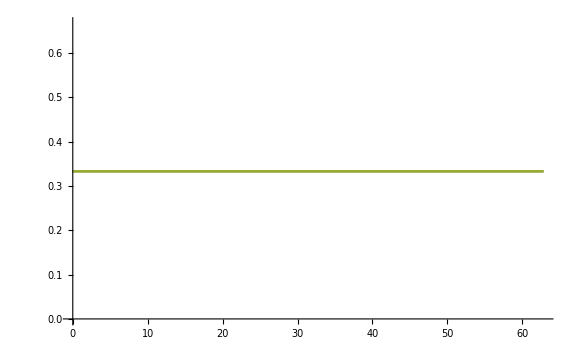
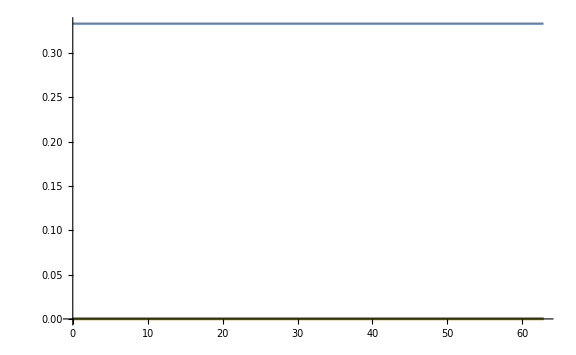

```mathematica
Remove[rinterp, rtable]
rtable=Import[".\\output\\r_index.mjson","ExpressionJSON"];
(* вынуждены определить функцию, чтобы зафиксировать порядок аргументов *)
rinterp[n1_, l1_, m1_, n2_, l2_, m2_,t_, α_, β_]:=ListInterpolation[rtable,{{ti,tf} ,{αi,αf}, {βi,βf},{2, neq},{ 0, neq-1}, {-neq, neq}, {2, nmax},{0, nmax-1}, {-nmax, nmax} }][t ,α, β, n1, l1, m1, n2, l2, m2];

calcSolution[α_, β_]:=Block[{solamp,nd,equations={},equationsall={},vars={},varsall={},initialcond={},tris={},triseq={},ampfuncall={},ampfunc={},amptris={}},
(*Задаем населенности*)
Print["Enter in calcSolution"];
varsall=Table[amp[n1,l1, m1], {n1, 2, neq}, {l1, 1, n1-1}, {m1, -l1, l1}];
tris={amp[3,0, 0]};
vars=Flatten[AppendTo[varsall,tris]];
Print["vars = ", vars];
(*Задаем уравнения для населенностей*)
equationsall=Table[{D[amp[n1,l1, m1] [t], t]==-I h (∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 rinterp[n1, l1, m1, n2, l2, m2, t ,α, β]*amp[n2,l2, m2][t]+rinterp[n1, l1, m1, 3, 0, 0, t ,α, β]*amp[3,0,0][t])},  {n1, 2, neq},{l1, 1, n1-1}, {m1, -l1, l1}];
(* Подготовим к выводу фиктивную таблицу *)
test = Table[{el[n1,l1,m1]},  {n1, 2, neq},{l1, 1, n1-1}, {m1, -l1, l1}];
Print["Table = ", test];
Print["Flatten table = ", Flatten[test]];
triseq={D[amp[3,0, 0] [t], t]==-I h (∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 rinterp[3, 0, 0, n2, l2, m2, t ,α, β]*amp[n2,l2, m2][t]+rinterp[3, 0, 0, 3, 0, 0, t ,α, β]*amp[3,0,0][t])};
equations=Flatten[AppendTo[equationsall,triseq]];
(* Print["equations = ", equations]; *)
(* Задаем начальные условия *)
initialcond={amp[2,1,-1][ti]==0.333,amp[2,1,0][ti]==0.333,amp[2,1,1][ti]==0.333,amp[3,1,-1][ti]==0,amp[3,1,0][ti]==0,amp[3,1,1][ti]==0,amp[3,2,-2][ti]==0,amp[3,2,-1][ti]==0,amp[3,2,0][ti]==0,amp[3,2,1][ti]==0,amp[3,2,2][ti]==0,amp[3,0,0][ti]==0};

(* Посмотрим, с чем мы приходим к фазе решения *)
(* Print[{equations,initialcond}//Flatten]; *)
(*Решаем систему*)
nd=NDSolve[{equations,initialcond}//Flatten, vars, {t, ti, tf}]//Flatten;
ampfuncall=Table[amp[n1,l1, m1][t]/.nd,{n1, 2, neq},{l1, 1, n1-1}, {m1, -l1, l1}];
amptris={amp[3,0,0][t]/.nd};
ampfunc=Flatten[AppendTo[ampfuncall,amptris]];
solamp=Table[ampfunc/.{t->tt}//Evaluate,{tt,ti,tf,dt}];

{solamp}]

time=Table[f,{f,ti,tf,dt}];
Table[
{Print[α];
elem =calcSolution[α, Pi/4.][[1]]//Flatten;
Print["Elem calculated"];

Arrray[Subscript[res, #]&,12] = Array[Take[elem,{#,Length[elem],12}]&, 12];

res1=Take[elem,{1,Length[elem],12}];
res2=Take[elem,{2,Length[elem],12}];
res3=Take[elem,{3,Length[elem],12}];
res4=Take[elem,{4,Length[elem],12}];
res5=Take[elem,{5,Length[elem],12}];
res6=Take[elem,{6,Length[elem],12}];
res7=Take[elem,{7,Length[elem],12}];
res8=Take[elem,{8,Length[elem],12}];
res9=Take[elem,{9,Length[elem],12}];
res10=Take[elem,{10,Length[elem],12}];
res11=Take[elem,{11,Length[elem],12}];
res12=Take[elem,{12,Length[elem],12}];

probres1=Transpose[{time, res1//Flatten}];
probres2=Transpose[{time, res2//Flatten}];
probres3=Transpose[{time, res3//Flatten}];
probres4=Transpose[{time, res4//Flatten}];
probres5=Transpose[{time, res5//Flatten}];
probres6=Transpose[{time, res6//Flatten}];
probres7=Transpose[{time, res7//Flatten}];
probres8=Transpose[{time, res8//Flatten}];
probres9=Transpose[{time, res9//Flatten}];
probres10=Transpose[{time, res10//Flatten}];
probres11=Transpose[{time, res11//Flatten}];
probres12=Transpose[{time, res12//Flatten}];



(*Export["probres1(angle="<>ToString[α]<>").csv",probres1,"Table","FieldSeparators"->";"];
Export["probres2(angle="<>ToString[α]<>").csv",probres2,"Table","FieldSeparators"->";"];
Export["probres3(angle="<>ToString[α]<>").csv",probres3,"Table","FieldSeparators"->";"];
Export["probres4(angle="<>ToString[α]<>").csv",probres4,"Table","FieldSeparators"->";"];*)

ListPlot[{Abs[probres1],Abs[probres2],Abs[probres3]},ImageSize->Large,Joined-> True, PlotRange->All]
ListPlot[{Abs[probres3],Abs[probres4],Abs[probres5],Abs[probres6],Abs[probres7],Abs[probres8],Abs[probres9],Abs[probres10],Abs[probres11],Abs[probres12]},ImageSize->Large,Joined-> True, PlotRange->All]
}
,
{α,αi,αf,dα}]
```

```mathematica
(* Закончили подсчет матричных элементов. Проверяем их *)
Print["n1=",Dynamic[n1], ", l1=",Dynamic[l1], ", m1=",Dynamic[m1], ", n2=",Dynamic[n2], ", l2=",Dynamic[l2], ", m2=",Dynamic[m2]];

TableForm[Table[∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 rinterp[n1, l1, m1, n2, l2, m2, ti ,Pi/4,Pi/4]*1+rinterp[n1, l1, m1, 3, 0, 0, ti,Pi/4,Pi/4]*1,{n1, 2, neq},{l1, 1, n1-1}, {m1, -l1, l1}],TableDepth->1]
∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 rinterp[3, 0, 0, n2, l2, m2, ti,Pi/4,Pi/4]*1+rinterp[3, 0, 0, 3, 0, 0, ti,Pi/4,Pi/4]*1
```

n1=, l1=, m1=, n2=, l2=, m2=

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1,0,0,1,2,3,1,2,3}.

General::stop: Further output of ListInterpolation::inhr will be suppressed during this calculation.

{{0.999934-0.00035237 ⅈ,0.999647-0.000656449 ⅈ,1.00009-0.000355588 ⅈ}}
{{-3382.26-18305. ⅈ,-18754.8-34638.3 ⅈ,5253.56-19197.8 ⅈ},{0.+0. ⅈ,18052.6-35531.1 ⅈ,34855.3+12745.7 ⅈ,-12763.4+20813.6 ⅈ,-23254.-70169.4 ⅈ}}

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1,0,0,1,2,3,1,2,3}.

General::stop: Further output of ListInterpolation::inhr will be suppressed during this calculation.

0.249862-0.00025168 ⅈ